Useful functions

```mathematica
Interpolate[data_, iδ_]:=Module[{},
	rdf = Flatten[Table[{{(is10-1)*iδ, (iη-1)*iδ}, data[[is10, iη]]}, {is10, 1, Length[data]}, {iη, 1, Length[data]}],1];
	Interpolation[rdf, InterpolationOrder->3]
]

InterpolateNoCutoff[data_, iδ_, ηmax_]:=Module[{},
rdf = Flatten[Table[{{(is10-1)*iδ , (iη-1)*iδ}, Piecewise[{{data[[is10- iη + Length[data], iη]], iη - Length[data]< is10 < iη}}, 1]}, {is10, -Length[data], Length[data]}, {iη, 1, Length[data]}],1];
	Interpolation[rdf, InterpolationOrder->3]
]

InputDir[δ_] := "/Users/brandonmanley/Desktop/PhD/moment_evolution/evolved_dipoles/largeNc&Nf/d"<>StringDrop[ToString[δ],2]<> "_ones/"

GetDipoles[inputDir_, δ_] := Module[{δString = "d"<> StringDrop[ToString[δ],2]},
Association[Table[ia -> Interpolate[Import[inputDir<>δString<>"_NcNf3_ones_"<>ia<>"_rc.dat"], δ], {ia, {"Q","G2", "I3", "I4", "I5"}}]]]

DBIntegrand[r_, p_, Q_, z_,x_,  Λ_, inds_, amp_, ampName_]:= Module[{xarg, yarg}, 
If[ampName==="N",
	xarg =  Log[r]; yarg =x, 
	xarg = Sqrt[3/(2π)]Log[1/(r^2 Λ^2)];  yarg = Sqrt[3/(2π)] Log[Q^2/(x Λ^2)];
];
(*r (p r)^inds[[1]](Q  Sqrt[z*(1-z)] r)^inds[[2]] BesselJ[inds[[3]], p r] BesselK[inds[[4]],Q  Sqrt[z*(1-z)] r] amp[xarg,yarg];*)
r (p r)^inds[[1]](Q  Sqrt[z*(1-z)] r)^inds[[2]] BesselK[inds[[4]],Q  Sqrt[z*(1-z)] r] amp[xarg,yarg]
]
DBTransform[p_, Q_, z_,x_,  Λ_, inds_, amp_, ampName_] := NIntegrate[DBIntegrand[r, p, Q, z,x,  Λ, inds, amp, ampName], {r,0.01, 1/Λ}]


aTT[p_, Q_,z_, dipoles_, x_: 0.01, Λ_:0.3, δ_ :0.05] := Module[{result=0},
	Ni1100 = DBTransform[p, Q, z, x, Λ, {1,1,0,0}, dipoles[δ]["N"], "N"];
	Qi1100 = DBTransform[p, Q, z, x, Λ, {1,1,0,0}, dipoles[δ]["Q"], "Q"];
	G2i1100 = DBTransform[p, Q, z, x, Λ, {1,1,0,0}, dipoles[δ]["G2"], "G2"];
	
	result = Ni1100*((1-2 z)^2 Qi1100 + 2(z^2+ (1-z)^2)G2i1100)
]
```

Import dipole files (polarized and unpolarized)
	- Note the the polarized amplitude arguments are 
	and the unpolarized amplitude arguments are

```mathematica
polamps =Association[Table[iδ->GetDipoles[InputDir[iδ], iδ], {iδ, {0.1, 0.08, 0.075, 0.0625, 0.05, 0.0375, 0.032}}]];

nfile = Import["/Users/brandonmanley/Desktop/PhD/rcbkdipole/build/bin/dipole_data/unpolarized_dipole_xmin0.010000_xmax0.000001.dat"];
namp = Interpolation[Table[{{nfile[[i, 2]], nfile[[i, 1]]}, nfile[[i, 3]]}, {i, 1, Length[nfile]}]];

amps = Association[Table[iδ->Association[polamps[iδ], "N"-> namp],  {iδ, {0.1, 0.08, 0.075, 0.0625, 0.05, 0.0375, 0.032}}]];
```

Play with double Bessel transform, defined as

```mathematica
<<MaTeX`
```

MaTeX::shdw: Symbol MaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

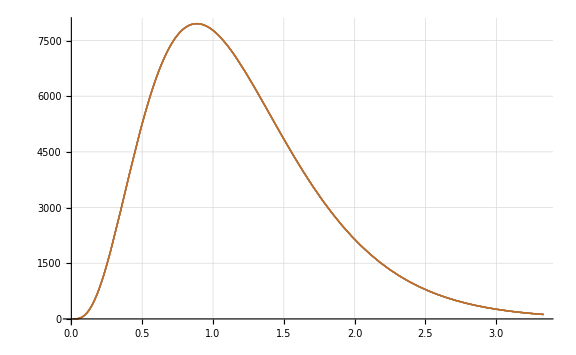
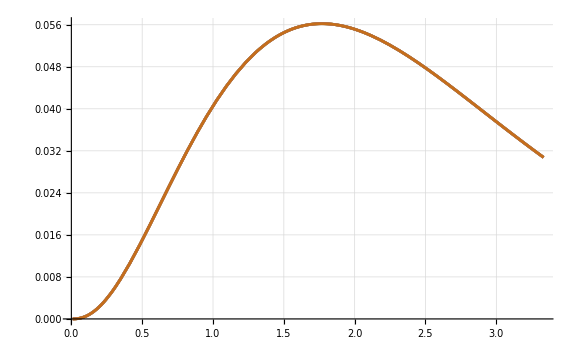

```mathematica
polintplot = Plot[Evaluate[Table[DBIntegrand[r, p, Sqrt[40],0.4,0.01, 0.3, {0,0,0,0}, amps[0.032]["Q"], "Q"], {p, {0.1, 2, 4, 6, 8, 10}}]], {r,0.01, 1/0.3},
PlotStyle->Table[{Thick, ColorData["Physical"][i/6]},{i,1,6}], PlotRange->All, AxesLabel->{MaTeX["r\\,\\, [\\mathrm{GeV}^{-1}]", Magnification->1.5]}, ImageSize->Large,
BaseStyle->{FontSize->16,FontFamily->"Times"}, GridLines->Automatic, PlotLegends->Placed[Table[MaTeX["p_\\perp="<>ToString[p]<>"\,\,\\mathrm{GeV}", Magnification->1.5],{p, {0.1, 2, 4, 6, 8, 10}}], Below],
PlotLabel->MaTeX["r J_0(p_{\\perp} r) K_0(\\sqrt{40} \\sqrt{0.4(1-0.4)}\\, r ) Q(r^2, x=0.01)", Magnification->1.5]
];

unpolintplot = Plot[Evaluate[Table[DBIntegrand[r, p, Sqrt[5],0.4,0.001, 0.3, {0,0,0,0}, amps[0.032]["N"], "N"], {p, {0.1, 2, 4, 6, 8, 10}}]], {r,0.01, 1/0.3},
PlotStyle->Table[{Thick, ColorData["Physical"][i/6]},{i,1,6}], PlotRange->All,AxesLabel->{MaTeX["r\\,\\, [\\mathrm{GeV}^{-1}]", Magnification->1.5]}, ImageSize->Large,
BaseStyle->{FontSize->16,FontFamily->"Times"}, GridLines->Automatic, PlotLegends->Placed[Table[MaTeX["p_\\perp="<>ToString[p]<>"\,\,\\mathrm{GeV}", Magnification->1.5],{p, {0.1, 2, 4, 6, 8, 10}}], Below],
PlotLabel->MaTeX["r J_0(p_{\\perp} r) K_0(\\sqrt{5} \\sqrt{0.4(1-0.4)}\\, r ) N(r^2, x=0.01)", Magnification->1.5], PlotRange->All
];

Row[{polintplot, unpolintplot}]
```

```mathematica
aTTs = Table[{Q^2, z, Table[{p, aTT[p, Q,z,amps]}, {p, 0.1,10, 0.1}]}, {Q, Sqrt[{20,25, 30, 35, 45}]},{z,{0.1, 0.2, 0.3, 0.4} }];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.808327}. NIntegrate obtained -1.43715×10^-7 and 3.61336×10^-13 for the integral and error estimates.

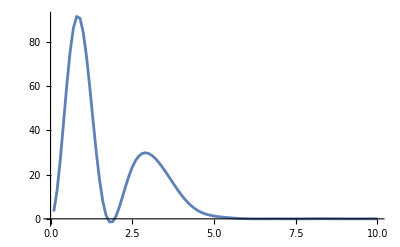

```mathematica
ListPlot[aTTs[[5,-1,3]], Joined->True]
```

```mathematica
polintplot = Plot[Evaluate[Table[DBIntegrand[r, p, Sqrt[40],0.4,0.01, 0.3, {1,1,0,0}, amps[0.032]["Q"], "Q"], {p, {0.1, 2, 4, 6, 8, 10}}]], {r,0.01, 1/0.3},
PlotStyle->Table[{Thick, ColorData["Physical"][i/6]},{i,1,6}], PlotRange->All, AxesLabel->{MaTeX["r\\,\\, [\\mathrm{GeV}^{-1}]", Magnification->1.5]}, ImageSize->Large,
BaseStyle->{FontSize->16,FontFamily->"Times"}, GridLines->Automatic, PlotLegends->Placed[Table[MaTeX["p_\\perp="<>ToString[p]<>"\,\,\\mathrm{GeV}", Magnification->1.5],{p, {0.1, 2, 4, 6, 8, 10}}], Below],
PlotLabel->MaTeX["r J_0(p_{\\perp} r) K_0(\\sqrt{40} \\sqrt{0.4(1-0.4)}\\, r ) Q(r^2, x=0.01)", Magnification->1.5]
];
```

```mathematica
DBvaryQz = Table[{Q^2, z, Table[{p, DBTransform[p, Q,0.2,0.01, 0.3, {0,0,0,0}, amps[0.1]["Q"], "Q"]}, {p, 0.1,10, 0.1}]}, {Q, Sqrt[{20,25, 30, 35, 45}]},{z,{0.1, 0.2, 0.3, 0.4} }];
```

```mathematica
DBvaryz = Table[{z, Table[{p, DBTransform[p, Sqrt[30],z,0.01, 0.3, {0,0,0,0}, polamps[0.1]["Q"], "polar"]}, {p, 0.1,10, 0.1}]}, {z, {0.1, 0.2, 0.3, 0.4}}];
```

```mathematica
DBvaryδ = Table[{δ, Table[{p, DBTransform[p, Sqrt[30],0.4,0.01, 0.3, {0,0,0,0}, polamps[δ]["Q"], "polar"]}, {p, 0.1,10, 0.1}]}, {δ, {0.1, 0.075, 0.05,0.032}}];
```

```mathematica
unDBvaryQz = Table[{z, Q^2, Table[{p, DBTransform[p, Q,z,0.01, 0.3, {0,0,0,0}, namp, "unpolar"]}, {p, 0.1,10, 0.1}]}, 
{Q, Sqrt[{20,25, 30, 35, 45}]},{z,{0.1, 0.2, 0.3, 0.4} }];
```

```mathematica
unDBvaryz = Table[{z, Table[{p, DBTransform[p, Sqrt[30],z,0.01, 0.3, {0,0,0,0}, namp, "unpolar"]}, {p, 0.1,10, 0.1}]}, {z, {0.1, 0.2, 0.3, 0.4}}];
```

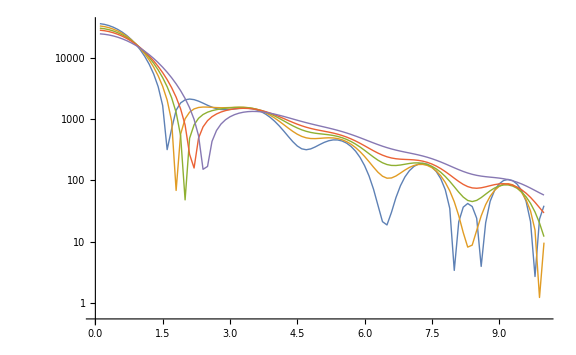
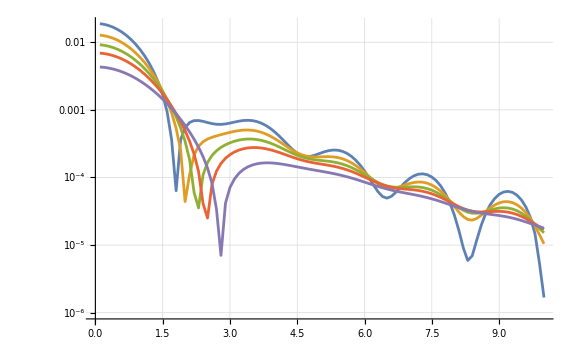

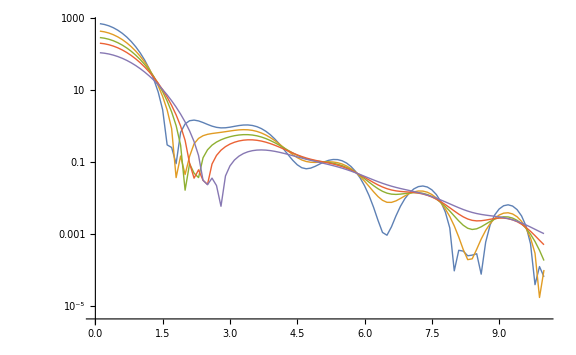

```mathematica
polQplot = ListLogPlot[Evaluate[Table[Table[{DBvaryQ[[i, 2, j, 1]],Abs[DBvaryQ[[i, 2, j, 2]]]}, {j, 1, Length[DBvaryQ[[i, 2]]]}], {i, 1, Length[DBvaryQ]}]],
PlotStyle->Table[{Thick, ColorData["Physical"][i/5]},{i,1,5}], PlotRange->All, AxesLabel->{MaTeX["p_{\\perp} \\,\\, [\\mathrm{GeV}]", Magnification->1.5]}, ImageSize->Large,Joined->True,
BaseStyle->{FontSize->16,FontFamily->"Times"}, GridLines->Automatic, PlotLegends->Placed[Table[MaTeX["Q^2 ="<>ToString[DBvaryQ[[i, 1]]]<>"\,\,\\mathrm{GeV}^2", Magnification->1.5],{i, 1, Length[DBvaryQ]}],  Below],
PlotLabel->MaTeX["Q_{(00)}^{(00)} (p_{\\perp}, z=0.2, Q; x=0.01, \\Lambda = 0.3\, \\mathrm{GeV})", Magnification->1.5]];

unpolQplot = ListLogPlot[Evaluate[Table[Table[{unDBvaryQ[[i, 2, j, 1]],Abs[unDBvaryQ[[i, 2, j, 2]]]}, {j, 1, Length[unDBvaryQ[[i, 2]]]}], {i, 1, Length[unDBvaryQ]}]],
PlotStyle->Table[{Thick, ColorData["Physical"][i/5]},{i,1,5}], PlotRange->All, AxesLabel->{MaTeX["p_{\\perp} \\,\\, [\\mathrm{GeV}]", Magnification->1.5]}, ImageSize->Large,Joined->True,
BaseStyle->{FontSize->16,FontFamily->"Times"}, GridLines->Automatic, PlotLegends->Placed[Table[MaTeX["Q^2 ="<>ToString[unDBvaryQ[[i, 1]]]<>"\,\,\\mathrm{GeV}^2", Magnification->1.5],{i, 1, Length[unDBvaryQ]}],  Below],
PlotLabel->MaTeX["N_{(00)}^{(00)} (p_{\\perp}, z=0.2, Q; x=0.01, \\Lambda = 0.3\, \\mathrm{GeV})", Magnification->1.5]];

mulQplot = ListLogPlot[Evaluate[Table[Table[{unDBvaryQ[[i, 2, j, 1]],Abs[unDBvaryQ[[i, 2, j, 2]] DBvaryQ[[i,2,j,2]]]}, {j, 1, Length[unDBvaryQ[[i, 2]]]}], {i, 1, Length[unDBvaryQ]}]],
PlotStyle->Table[{Thick, ColorData["Physical"][i/5]},{i,1,5}], PlotRange->All, AxesLabel->{MaTeX["p_{\\perp} \\,\\, [\\mathrm{GeV}]", Magnification->1.5]}, ImageSize->Large,Joined->True,
BaseStyle->{FontSize->16,FontFamily->"Times"}, GridLines->Automatic,PlotLegends->Placed[Table[MaTeX["Q^2 ="<>ToString[unDBvaryQ[[i, 1]]]<>"\,\,\\mathrm{GeV}^2", Magnification->1.5],{i, 1, Length[unDBvaryQ]}],  Below],
PlotLabel->MaTeX["N*Q_{(00)}^{(00)} (p_{\\perp}, z=0.2, Q; x=0.01, \\Lambda = 0.3\, \\mathrm{GeV})", Magnification->1.5]];

Row[{polQplot, unpolQplot}]
mulQplot
```

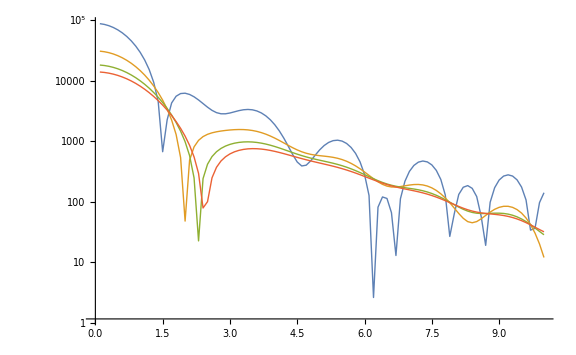
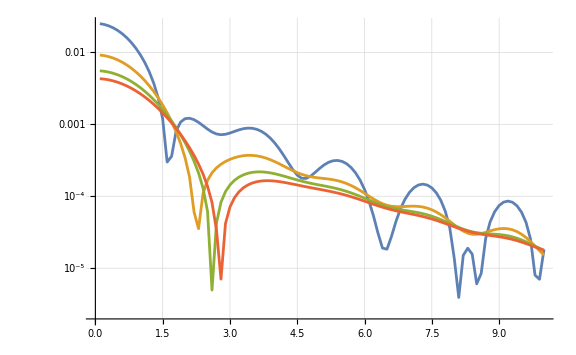

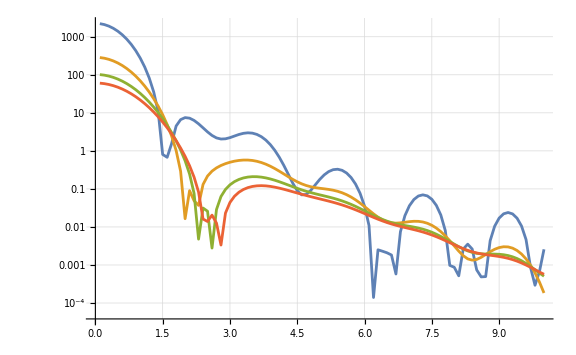

```mathematica
polzplot = ListLogPlot[Evaluate[Table[Table[{DBvaryz[[i, 2, j, 1]],Abs[DBvaryz[[i, 2, j, 2]]]}, {j, 1, Length[DBvaryz[[i, 2]]]}], {i, 1, Length[DBvaryz]}]],
PlotStyle->Table[{Thick, ColorData["Physical"][i/5]},{i,1,5}], PlotRange->All, AxesLabel->{MaTeX["p_{\\perp} \\,\\, [\\mathrm{GeV}]", Magnification->1.5]}, ImageSize->Large,Joined->True,
BaseStyle->{FontSize->16,FontFamily->"Times"}, GridLines->Automatic, PlotLegends->Placed[Table[MaTeX["z ="<>ToString[DBvaryz[[i, 1]]], Magnification->1.5],{i, 1, Length[DBvaryz]}],Below],
PlotLabel->MaTeX["Q_{(00)}^{(00)} (p_{\\perp}, z, Q^2=30\\,\\,\\mathrm{GeV}^2; x=0.01, \\Lambda = 0.3\\, \\mathrm{GeV})", Magnification->1.5]];

unpolzplot = ListLogPlot[Evaluate[Table[Table[{unDBvaryz[[i, 2, j, 1]],Abs[unDBvaryz[[i, 2, j, 2]]]}, {j, 1, Length[unDBvaryz[[i, 2]]]}], {i, 1, Length[unDBvaryz]}]],
PlotStyle->Table[{Thick, ColorData["Physical"][i/5]},{i,1,5}], PlotRange->All, AxesLabel->{MaTeX["p_{\\perp} \\,\\, [\\mathrm{GeV}]", Magnification->1.5]}, ImageSize->Large,Joined->True,
BaseStyle->{FontSize->16,FontFamily->"Times"}, GridLines->Automatic, PlotLegends->Placed[Table[MaTeX["z ="<>ToString[unDBvaryz[[i, 1]]], Magnification->1.5],{i, 1, Length[unDBvaryz]}],Below],
PlotLabel->MaTeX["N_{(00)}^{(00)} (p_{\\perp}, z, Q^2=30\\,\\,\\mathrm{GeV}^2; x=0.01, \\Lambda = 0.3\\, \\mathrm{GeV})", Magnification->1.5]];

mulzplot = ListLogPlot[Evaluate[Table[Table[{unDBvaryz[[i, 2, j, 1]],Abs[unDBvaryz[[i, 2, j, 2]]*DBvaryz[[i, 2, j, 2]]]}, {j, 1, Length[unDBvaryz[[i, 2]]]}], {i, 1, Length[unDBvaryz]}]],
PlotStyle->Table[{Thick, ColorData["Physical"][i/5]},{i,1,5}], PlotRange->All, AxesLabel->{MaTeX["p_{\\perp} \\,\\, [\\mathrm{GeV}]", Magnification->1.5]}, ImageSize->Large,Joined->True,
BaseStyle->{FontSize->16,FontFamily->"Times"}, GridLines->Automatic, PlotLegends->Placed[Table[MaTeX["z ="<>ToString[unDBvaryz[[i, 1]]], Magnification->1.5],{i, 1, Length[unDBvaryz]}],Below],
PlotLabel->MaTeX["N*Q_{(00)}^{(00)} (p_{\\perp}, z, Q^2=30\\,\\,\\mathrm{GeV}^2; x=0.01, \\Lambda = 0.3\\, \\mathrm{GeV})", Magnification->1.5]];


Row[{polzplot, unpolzplot}]
mulzplot
```

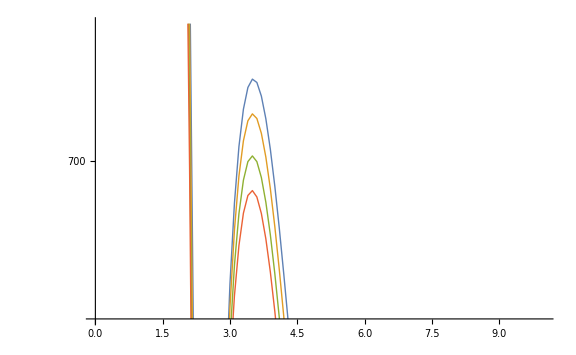

```mathematica
ListLogPlot[Evaluate[Table[Table[{DBvaryδ[[i, 2, j, 1]],Abs[DBvaryδ[[i, 2, j, 2]]]}, {j, 1, Length[DBvaryδ[[i, 2]]]}], {i, 1, Length[DBvaryδ]}]],
PlotStyle->Table[{Thick, ColorData["Physical"][i/4]},{i,1,4}], PlotRange->{600, 800}, AxesLabel->{MaTeX["p_{\\perp} \\,\\, [\\mathrm{GeV}]", Magnification->1.5]}, ImageSize->Large,Joined->True,
BaseStyle->{FontSize->16,FontFamily->"Times"}, GridLines->Automatic, PlotLegends->Table[MaTeX["\\delta ="<>ToString[DBvaryδ[[i, 1]]], Magnification->1.5],{i, 1, Length[DBvaryδ]}],
PlotLabel->MaTeX["Q_{(00)}^{(00)} (p_{\\perp}, z=0.4, Q^2=30\\,\\,\\mathrm{GeV}^2; x=0.01, \\Lambda = 0.3\\, \\mathrm{GeV})", Magnification->1.5]]
```

```mathematica
BesselApprox[ν_, x_, xcrit_, α_] :=
α Piecewise[{
{(Series[BesselJ[ν, y], {y,0,3}]//Normal)/.{y->x} , x<xcrit},
{ Sqrt[2/(π x)] + ((Series[BesselJ[ν, y], {y,0,3}]//Normal)/.{y->xcrit}) - ( Sqrt[2/(π y)] /.{y->xcrit}), x >= xcrit}
}]
```

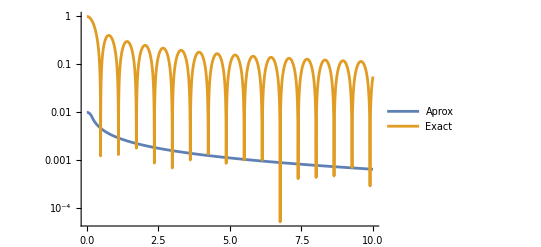

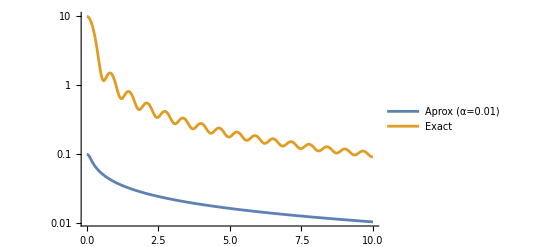

```mathematica
LogPlot[{Abs[BesselApprox[0, 5 x, 1, 0.01]],Abs[BesselJ[0,5 x]]}, {x,0,10}, PlotLegends->{"Aprox", "Exact"}, PlotRange->All]
LogPlot[{NIntegrate[BesselApprox[0, p x, 1, 0.01], {x,0,10}], NIntegrate[BesselJ[0,p x], {x,0,10}]}, {p,0,10}, PlotLegends->{"Aprox (α=0.01)", "Exact"}, PlotRange->All]
```

0.4

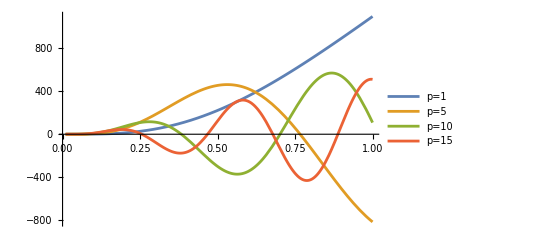

```mathematica
Q = Sqrt[5];
x = 0.01;
z=0.4
Plot[{r BesselJ[1, 1 r] BesselK[1,Q  Sqrt[z*(1-z)] r] polAmps[[1]][Sqrt[3/(2π)]Log[1/r^2], Sqrt[3/(2π)] Log[Q^2/x]] ,
r BesselJ[1, 5 r] BesselK[1,Q  Sqrt[z*(1-z)] r] polAmps[[1]][Sqrt[3/(2π)]Log[1/r^2], Sqrt[3/(2π)] Log[Q^2/x]] ,
r BesselJ[1, 10 r] BesselK[1,Q  Sqrt[z*(1-z)] r] polAmps[[1]][Sqrt[3/(2π)]Log[1/r^2], Sqrt[3/(2π)] Log[Q^2/x]],
r BesselJ[1, 15 r] BesselK[1,Q  Sqrt[z*(1-z)] r] polAmps[[1]][Sqrt[3/(2π)]Log[1/r^2], Sqrt[3/(2π)] Log[Q^2/x]]}
, {r,10^-2,1 }, PlotLegends->{"p=1", "p=5", "p=10", "p=15"}, PlotStyle->Thick]
```

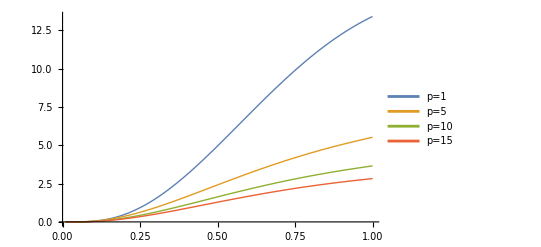

```mathematica
Plot[{r BesselApprox[0, 1 r, 1, 0.01] BesselK[0,Q  Sqrt[z*(1-z)] r] polAmps[[1]][Sqrt[3/(2π)]Log[1/r^2], Sqrt[3/(2π)] Log[Q^2/x]] ,
r BesselApprox[0, 5 r, 1, 0.01] BesselK[0,Q  Sqrt[z*(1-z)] r] polAmps[[1]][Sqrt[3/(2π)]Log[1/r^2], Sqrt[3/(2π)] Log[Q^2/x]] ,
r BesselApprox[0, 10 r, 1, 0.01] BesselK[0,Q  Sqrt[z*(1-z)] r] polAmps[[1]][Sqrt[3/(2π)]Log[1/r^2], Sqrt[3/(2π)] Log[Q^2/x]],
r BesselApprox[0, 15 r, 1, 0.01] BesselK[0,Q  Sqrt[z*(1-z)] r] polAmps[[1]][Sqrt[3/(2π)]Log[1/r^2], Sqrt[3/(2π)] Log[Q^2/x]]}
, {r,10^-2,1 }, PlotLegends->{"p=1", "p=5", "p=10", "p=15"}, PlotStyle->Thick, PlotRange->All]
```

```mathematica
Integrate[Cos[ϕ]^2,{ϕ,0,2π}]
```

π